# Industrial Robotics - Exam 15/01/2021

```mathematica
ClearAll["Global`*"]
```

-Graphics-
The 3 degrees of freedom robot in the picture is composed of two revolute joints and a prismatic joint. The rotation  is performed about axis ,  about axis  and the translation  (only positive) along axis . When  axes  and  are aligned, when  axes  and  are aligned, when  the end effector E is at a distance  from the origin of frame 2.

### 1) Find the matrix M03.

```mathematica
MrotZtrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
```

Focus on RF1:

```mathematica
O1={0,0,L1,1};
M01p=MrotZtrasl[q1[t],O1];
M1p1=Transpose[{{0,1,0,0},{0,0,1,0},{1,0,0,0},{0,0,0,1}}];
M01=M01p.M1p1;
M01//MatrixForm
```

(-Sin[q1[t]] | 0 | Cos[q1[t]] | 0
Cos[q1[t]] | 0 | Sin[q1[t]] | 0
0 | 1 | 0 | L1
0 | 0 | 0 | 1)

Focus on RF2:

```mathematica
O2rf1={0,0,L2,1};
M12p=MrotZtrasl[q2[t],O2rf1];
M2p2=Transpose[{{0,1,0,0},{0,0,1,0},{1,0,0,0},{0,0,0,1}}];
M12=M12p.M2p2;
M02=M01.M12;
M02//MatrixForm
```

(Sin[q1[t]] Sin[q2[t]] | Cos[q1[t]] | -Cos[q2[t]] Sin[q1[t]] | L2 Cos[q1[t]]
-Cos[q1[t]] Sin[q2[t]] | Sin[q1[t]] | Cos[q1[t]] Cos[q2[t]] | L2 Sin[q1[t]]
Cos[q2[t]] | 0 | Sin[q2[t]] | L1
0 | 0 | 0 | 1)

Focus on RF3:

```mathematica
O3rf2={0,0,L3+q3[t],1};
M23=MrotZtrasl[0,O3rf2];
M03=M02.M23;
M03//MatrixForm
```

(Sin[q1[t]] Sin[q2[t]] | Cos[q1[t]] | -Cos[q2[t]] Sin[q1[t]] | L2 Cos[q1[t]]-Cos[q2[t]] (L3+q3[t]) Sin[q1[t]]
-Cos[q1[t]] Sin[q2[t]] | Sin[q1[t]] | Cos[q1[t]] Cos[q2[t]] | Cos[q1[t]] Cos[q2[t]] (L3+q3[t])+L2 Sin[q1[t]]
Cos[q2[t]] | 0 | Sin[q2[t]] | L1+(L3+q3[t]) Sin[q2[t]]
0 | 0 | 0 | 1)

### 2) Find and explain the singular configurations.

Position EE

```mathematica
EE=M03[[;;,4]];
EE=M03.{0,0,0,1};(*alternativa*)
EE//MatrixForm
```

(L2 Cos[q1[t]]-Cos[q2[t]] (L3+q3[t]) Sin[q1[t]]
Cos[q1[t]] Cos[q2[t]] (L3+q3[t])+L2 Sin[q1[t]]
L1+(L3+q3[t]) Sin[q2[t]]
1)

Jacobian

```mathematica
Jac=Simplify[D[EE[[1;;3]],{{q1[t],q2[t],q3[t]}}]];
Jac//MatrixForm
```

(-Cos[q1[t]] Cos[q2[t]] (L3+q3[t])-L2 Sin[q1[t]] | (L3+q3[t]) Sin[q1[t]] Sin[q2[t]] | -Cos[q2[t]] Sin[q1[t]]
L2 Cos[q1[t]]-Cos[q2[t]] (L3+q3[t]) Sin[q1[t]] | -Cos[q1[t]] (L3+q3[t]) Sin[q2[t]] | Cos[q1[t]] Cos[q2[t]]
0 | Cos[q2[t]] (L3+q3[t]) | Sin[q2[t]])

Singular Configurations

```mathematica
detJac=Simplify[Det[Jac]]
```

Cos[q2[t]] (L3+q3[t])^2

```mathematica
q2Singular=Solve[detJac==0,q2[t]]
```

{{q2[t]→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{q2[t]→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]}}

```mathematica
q3Singular=Solve[detJac==0,q3[t]]
```

{{q3[t]→-L3},{q3[t]→-L3}}

```mathematica
Rot03=M03[[1;;3,1;;3]];
JacEE=Simplify[Transpose[Rot03].Jac];
JacEE/.q2[t]->π/2//MatrixForm
```

(-L2 | L3+q3[t] | 0
0 | 0 | 0
0 | 0 | 1)

When q_2=π/2, col1 and col2 of the Jacobian are linearly dependent, therefore the rank drops. In this configuration, no velocity can be produced at the end effector along .

```mathematica
JacEE/.q2[t]->-π/2//MatrixForm
```

(L2 | L3+q3[t] | 0
0 | 0 | 0
0 | 0 | 1)

When =-π/2, the situation is analogous to the previous one.

```mathematica
JacEE/.q3[t]->-L3//MatrixForm
```

(-L2 Sin[q2[t]] | 0 | 0
0 | 0 | 0
L2 Cos[q2[t]] | 0 | 1)

When =-L3, we would also lose movement along , but the robot impose , therefore, we will never encounter this singularity.

### 3) Find the joint coordinates compatible with the robot kinematics related to the two following configurations (assuming L1=L2=0.8m, L3=0.5m): • E coordinates in frame 0 are (1,0,1), selecting the solution with minimum variation of joint coordinates from zero • E coordinates in frame 0 are with axis x3 parallel and opposite to z0 • Calculate the constant acceleration joint time histories (zero initial and final velocity) to move each joint from the first to the second configuration (no velocity limits) in 1s.

```mathematica
lenData={L1->0.8,L2->0.8,L3->0.5};
```

```mathematica
EEx=EE[[1]];EEy=EE[[2]];EEz=EE[[3]];
EExNum=EEx/.lenData
EEyNum=EEy/.lenData
EEzNum=EEz/.lenData
```

0.8 Cos[q1[t]]-Cos[q2[t]] (0.5+q3[t]) Sin[q1[t]]

Cos[q1[t]] Cos[q2[t]] (0.5+q3[t])+0.8 Sin[q1[t]]

0.8+(0.5+q3[t]) Sin[q2[t]]

```mathematica
allKinematicSol1=Solve[{EExNum==1,EEyNum==0,EEzNum==1},{q1[t],q2[t],q3[t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q1[t]→-0.643501,q2[t]→-2.81984,q3[t]→-1.13246},{q1[t]→0.643501,q2[t]→-0.321751,q3[t]→-1.13246},{q1[t]→-0.643501,q2[t]→0.321751,q3[t]→0.132456},{q1[t]→0.643501,q2[t]→2.81984,q3[t]→0.132456}}

We immediately discard the solutions with . The we pick the one with minimum variation of joint coordinates from zero.

```mathematica
KinematicSol1=allKinematicSol1[[3]](*Pick sol3*)
```

{q1[t]→-0.643501,q2[t]→0.321751,q3[t]→0.132456}

```mathematica
x3UnitRF3={1,0,0,0};
x3UnitRF0=M03.x3UnitRF3;
x3UnitRF0=x3UnitRF0[[1;;3]];
x3UnitRF0//MatrixForm
M03[[1;;3,1]] (*Or use M03 col directly*)
```

(Sin[q1[t]] Sin[q2[t]]
-Cos[q1[t]] Sin[q2[t]]
Cos[q2[t]])

{Sin[q1[t]] Sin[q2[t]],-Cos[q1[t]] Sin[q2[t]],Cos[q2[t]]}

```mathematica
allKinematicSol2=Solve[{EExNum==0,EEyNum==-1.4,x3UnitRF0[[3]]==-1},{q1[t],q2[t],q3[t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q1[t]→-2.53335,q2[t]→-3.14159,q3[t]→-1.64891},{q1[t]→-2.53335,q2[t]→3.14159,q3[t]→-1.64891},{q1[t]→-0.608246,q2[t]→-3.14159,q3[t]→0.648913},{q1[t]→-0.608246,q2[t]→3.14159,q3[t]→0.648913}}

```mathematica
KinematicSol2=allKinematicSol2[[4]]
```

{q1[t]→-0.608246,q2[t]→3.14159,q3[t]→0.648913}

Define triangular profiles.

```mathematica
q1i=q1[t]/.KinematicSol1 (*Initial conds*)
q2i=q2[t]/.KinematicSol1
q3i=q3[t]/.KinematicSol1
q1f=q1[t]/.KinematicSol2 (*Final conds*)
q2f=q2[t]/.KinematicSol2
q3f=q3[t]/.KinematicSol2
```

-0.643501

0.321751

0.132456

-0.608246

3.14159

0.648913

```mathematica
baseProfile=Piecewise[{{qin+1/2((4(qfin-qin))/T^2)t^2,0<=t<=T/2},{qfin-1/2((4(qfin-qin))/T^2)(T-t)^2,T/2<t<=T}}]
```

Piecewise[{{qin+(2 (qfin-qin) t^2)/T^2, 0≤t≤T/2}, {qfin-(2 (qfin-qin) (-t+T)^2)/T^2, T/2<t≤T}, {0, True}}]

```mathematica
q1Profile=baseProfile/.qin->q1i/.qfin->q1f/.T->1
```

Piecewise[{{-0.643501+0.0705111 t^2, 0≤t≤1/2}, {-0.608246-0.0705111 (1-t)^2, 1/2<t≤1}, {0, True}}]

```mathematica
q2Profile=baseProfile/.qin->q2i/.qfin->q2f/.T->1
```

Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]

```mathematica
q3Profile=baseProfile/.qin->q3i/.qfin->q3f/.T->1
```

Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]

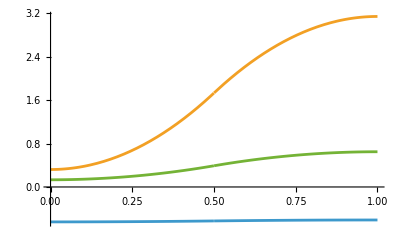

```mathematica
Plot[{q1Profile,q2Profile,q3Profile},{t,0,1}]
```

### 4) Assume that joint 2 can produce a maximum velocity of 3 rad/s and is commanded with the same acceleration and deceleration found in point 3. Find and explain the minimum overall repositioning time.

We have a saturation variable. Check if .

```mathematica
vPeak2=√((4(Δq)^2)/T^2)/.Δq->(q2f-q2i)/.T->1
```

5.63968

So  surpasses vMax=3 rad/s. We can find the new time using the formula:

```mathematica
Δt[Δq_,vMax_,A_,D_]:=Δq/vMax+1/2 vMax (A+D)/(A D);
```

```mathematica
acc=(4(q2f-q2i))/1^2
```

11.2794

```mathematica
newT2=Δt[q2f-q2i,3,acc,acc]
```

1.20592

### 5) Links 1 and 2 can be approximated with lumped masses m1 and m2 located in G1 and G2 at half the length L1 and L2 of each link; link 3 is approximated by a lumped mass m3 located in G3 = E . The gravity force is present along–z0 . • Calculate and plot (with scales) the torque and force time histories required to perform the motion from the initial to the final configuration of point 2 with no velocity limit, assuming m1 = 10 kg, m2 = 10 kg, m3 = 3 kg.

```mathematica
massData={m1->10,m2->10,m3->3,g->9.81};
```

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];
W02=Simplify[D[M02,t].Inverse[M02]];
W03=Simplify[D[M03,t].Inverse[M03]];
```

```mathematica
J11={{0,0,0,0},{0,m1(-L1/2)^2,0,m1(-L1/2)},{0,0,0,0},{0,m1(-L1/2),0,m1}};
J11//MatrixForm
```

(0 | 0 | 0 | 0
0 | (L1^2 m1)/4 | 0 | -(L1 m1)/2
0 | 0 | 0 | 0
0 | -(L1 m1)/2 | 0 | m1)

```mathematica
J22={{0,0,0,0},{0,m2(-L2/2)^2,0,m2(-L2/2)},{0,0,0,0},{0,m2(-L2/2),0,m2}};
J22//MatrixForm
```

(0 | 0 | 0 | 0
0 | (L2^2 m2)/4 | 0 | -(L2 m2)/2
0 | 0 | 0 | 0
0 | -(L2 m2)/2 | 0 | m2)

```mathematica
J33={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,m3}};
J33//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | m3)

```mathematica
J10=Simplify[M01.J11.Transpose[M01]];
J20=Simplify[M02.J22.Transpose[M02]];
J30=Simplify[M03.J33.Transpose[M03]];
```

Kinetic energy.

```mathematica
T1=Simplify[1/2 Tr[W01.J10.Transpose[W01]]]
```

0

```mathematica
T2=Simplify[1/2 Tr[W02.J20.Transpose[W02]]]
```

1/8 L2^2 m2 q1'[t]^2

```mathematica
T3=Simplify[1/2 Tr[W03.J30.Transpose[W03]]]
```

1/4 m3 ((2 L2^2+L3^2+L3^2 Cos[2 q2[t]]+4 L3 Cos[q2[t]]^2 q3[t]+2 Cos[q2[t]]^2 q3[t]^2) q1'[t]^2-4 L2 q1'[t] ((L3+q3[t]) Sin[q2[t]] q2'[t]-Cos[q2[t]] q3'[t])+2 ((L3+q3[t])^2 q2'[t]^2+q3'[t]^2))

Potential energy.

```mathematica
Hg1={{0,0,0,0},{0,0,0,0},{0,0,0,-g},{0,0,0,0}};
Hg2=Hg1; Hg3=Hg1;
Hg1//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -g
0 | 0 | 0 | 0)

```mathematica
Ug1=Tr[-Hg1.J10]
```

(g L1 m1)/2

```mathematica
Ug2=Tr[-Hg2.J20]
```

g L1 m2

```mathematica
Ug3=Tr[-Hg3.J30]
```

g m3 (L1+(L3+q3[t]) Sin[q2[t]])

Lagrangian term.

```mathematica
Lagr=Simplify[T1+T2+T3-Ug1-Ug2-Ug3]
```

1/8 (-4 g L1 m1-8 g L1 m2-8 g m3 (L1+(L3+q3[t]) Sin[q2[t]])+L2^2 m2 q1'[t]^2+2 m3 ((2 L2^2+L3^2+L3^2 Cos[2 q2[t]]+4 L3 Cos[q2[t]]^2 q3[t]+2 Cos[q2[t]]^2 q3[t]^2) q1'[t]^2-4 L2 q1'[t] ((L3+q3[t]) Sin[q2[t]] q2'[t]-Cos[q2[t]] q3'[t])+2 ((L3+q3[t])^2 q2'[t]^2+q3'[t]^2)))

Equation 1:

```mathematica
dLagrdq1dotdt=Simplify[D[D[Lagr,q1'[t]],t]]
```

1/4 (-4 L2 m3 Cos[q2[t]] (L3+q3[t]) q2'[t]^2-8 L2 m3 Sin[q2[t]] q2'[t] q3'[t]-8 m3 Cos[q2[t]] (L3+q3[t]) q1'[t] ((L3+q3[t]) Sin[q2[t]] q2'[t]-Cos[q2[t]] q3'[t])+L2^2 m2 q1''[t]+4 L2^2 m3 q1''[t]+2 L3^2 m3 q1''[t]+2 L3^2 m3 Cos[2 q2[t]] q1''[t]+8 L3 m3 Cos[q2[t]]^2 q3[t] q1''[t]+4 m3 Cos[q2[t]]^2 q3[t]^2 q1''[t]-4 L2 L3 m3 Sin[q2[t]] q2''[t]-4 L2 m3 q3[t] Sin[q2[t]] q2''[t]+4 L2 m3 Cos[q2[t]] q3''[t])

```mathematica
dLagrdq1=Simplify[D[Lagr,q1[t]]]
```

0

Equation 2:

```mathematica
dLagrdq2dotdt=Simplify[D[D[Lagr,q2'[t]],t]]
```

m3 (-L2 q1'[t] (Cos[q2[t]] (L3+q3[t]) q2'[t]+Sin[q2[t]] q3'[t])+(L3+q3[t]) (2 q2'[t] q3'[t]-L2 Sin[q2[t]] q1''[t]+(L3+q3[t]) q2''[t]))

```mathematica
dLagrdq2=Simplify[D[Lagr,q2[t]]]
```

1/4 m3 (-4 g Cos[q2[t]] (L3+q3[t])-2 (L3+q3[t])^2 Sin[2 q2[t]] q1'[t]^2-4 L2 q1'[t] (Cos[q2[t]] (L3+q3[t]) q2'[t]+Sin[q2[t]] q3'[t]))

Equation 3:

```mathematica
dLagrdq3dotdt=Simplify[D[D[Lagr,q3'[t]],t]]
```

m3 (-L2 Sin[q2[t]] q1'[t] q2'[t]+L2 Cos[q2[t]] q1''[t]+q3''[t])

```mathematica
dLagrdq3=Simplify[D[Lagr,q3[t]]]
```

m3 (-g Sin[q2[t]]+Cos[q2[t]]^2 (L3+q3[t]) q1'[t]^2-L2 Sin[q2[t]] q1'[t] q2'[t]+(L3+q3[t]) q2'[t]^2)

Equations of motion

```mathematica
equation1=dLagrdq1dotdt-dLagrdq1-C1//Simplify
```

1/4 (-4 C1-4 L2 m3 Cos[q2[t]] (L3+q3[t]) q2'[t]^2-8 L2 m3 Sin[q2[t]] q2'[t] q3'[t]-8 m3 Cos[q2[t]] (L3+q3[t]) q1'[t] ((L3+q3[t]) Sin[q2[t]] q2'[t]-Cos[q2[t]] q3'[t])+L2^2 m2 q1''[t]+4 L2^2 m3 q1''[t]+2 L3^2 m3 q1''[t]+2 L3^2 m3 Cos[2 q2[t]] q1''[t]+8 L3 m3 Cos[q2[t]]^2 q3[t] q1''[t]+4 m3 Cos[q2[t]]^2 q3[t]^2 q1''[t]-4 L2 L3 m3 Sin[q2[t]] q2''[t]-4 L2 m3 q3[t] Sin[q2[t]] q2''[t]+4 L2 m3 Cos[q2[t]] q3''[t])

```mathematica
equation2=dLagrdq2dotdt-dLagrdq2-C2//Simplify
```

-C2+g m3 Cos[q2[t]] (L3+q3[t])+1/2 m3 (L3+q3[t])^2 Sin[2 q2[t]] q1'[t]^2+m3 (L3+q3[t]) (2 q2'[t] q3'[t]-L2 Sin[q2[t]] q1''[t]+(L3+q3[t]) q2''[t])

```mathematica
equation3=dLagrdq3dotdt-dLagrdq3-F3//Simplify
```

-F3+g m3 Sin[q2[t]]-m3 Cos[q2[t]]^2 (L3+q3[t]) q1'[t]^2-m3 (L3+q3[t]) q2'[t]^2+L2 m3 Cos[q2[t]] q1''[t]+m3 q3''[t]

Inverse Dynamics

```mathematica
C1dyn=C1/.Flatten[Solve[equation1==0,C1]]
```

1/4 (-8 L3^2 m3 Cos[q2[t]] Sin[q2[t]] q1'[t] q2'[t]-16 L3 m3 Cos[q2[t]] q3[t] Sin[q2[t]] q1'[t] q2'[t]-8 m3 Cos[q2[t]] q3[t]^2 Sin[q2[t]] q1'[t] q2'[t]-4 L2 L3 m3 Cos[q2[t]] q2'[t]^2-4 L2 m3 Cos[q2[t]] q3[t] q2'[t]^2+8 L3 m3 Cos[q2[t]]^2 q1'[t] q3'[t]+8 m3 Cos[q2[t]]^2 q3[t] q1'[t] q3'[t]-8 L2 m3 Sin[q2[t]] q2'[t] q3'[t]+L2^2 m2 q1''[t]+4 L2^2 m3 q1''[t]+2 L3^2 m3 q1''[t]+2 L3^2 m3 Cos[2 q2[t]] q1''[t]+8 L3 m3 Cos[q2[t]]^2 q3[t] q1''[t]+4 m3 Cos[q2[t]]^2 q3[t]^2 q1''[t]-4 L2 L3 m3 Sin[q2[t]] q2''[t]-4 L2 m3 q3[t] Sin[q2[t]] q2''[t]+4 L2 m3 Cos[q2[t]] q3''[t])

```mathematica
C2dyn=C2/.Flatten[Solve[equation2==0,C2]]
```

g m3 Cos[q2[t]] (L3+q3[t])+1/2 m3 (L3+q3[t])^2 Sin[2 q2[t]] q1'[t]^2+m3 (L3+q3[t]) (2 q2'[t] q3'[t]-L2 Sin[q2[t]] q1''[t]+(L3+q3[t]) q2''[t])

```mathematica
F3dyn=F3/.Flatten[Solve[equation3==0,F3]]
```

g m3 Sin[q2[t]]-L3 m3 Cos[q2[t]]^2 q1'[t]^2-m3 Cos[q2[t]]^2 q3[t] q1'[t]^2-L3 m3 q2'[t]^2-m3 q3[t] q2'[t]^2+L2 m3 Cos[q2[t]] q1''[t]+m3 q3''[t]

Plot Torques (& Forces) Profiles

```mathematica
C1dynNum=C1dyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

1/4 (15.58 (Piecewise[{{0, t<0}, {0.141022, 0<t<1/2}, {-0.141022, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+1.5 Cos[2 (Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}])] (Piecewise[{{0, t<0}, {0.141022, 0<t<1/2}, {-0.141022, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+12. Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]^2 (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]) (Piecewise[{{0, t<0}, {0.141022, 0<t<1/2}, {-0.141022, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+12 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]^2 (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}])^2 (Piecewise[{{0, t<0}, {0.141022, 0<t<1/2}, {-0.141022, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+9.6 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (Piecewise[{{0, t<0}, {2.06583, 0<t<1/2}, {-2.06583, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+12. Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]^2 (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {2.06583 t, 0<t<1/2}, {-1.03291 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+24 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]^2 (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]) (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {2.06583 t, 0<t<1/2}, {-1.03291 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])-4.8 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])^2-9.6 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]) (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])^2-4.8 (Piecewise[{{0, t<0}, {11.2794, 0<t<1/2}, {-11.2794, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]-9.6 (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]) (Piecewise[{{0, t<0}, {11.2794, 0<t<1/2}, {-11.2794, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]-6. Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]-24. Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]) (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]-24 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}])^2 (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]-19.2 (Piecewise[{{0, t<0}, {2.06583 t, 0<t<1/2}, {-1.03291 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]])

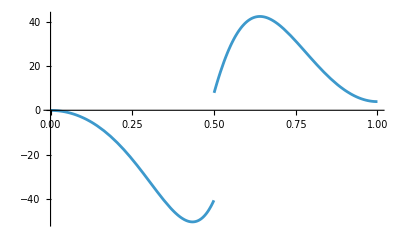

```mathematica
Plot[C1dynNum,{t,0,1}]
```

```mathematica
C2dynNum=C2dyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

29.43 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (0.5+(Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]))+3 (0.5+(Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}])) ((0.5+(Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}])) (Piecewise[{{0, t<0}, {11.2794, 0<t<1/2}, {-11.2794, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+2 (Piecewise[{{0, t<0}, {2.06583 t, 0<t<1/2}, {-1.03291 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])-0.8 (Piecewise[{{0, t<0}, {0.141022, 0<t<1/2}, {-0.141022, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}]) Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]])+3/2 (0.5+(Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]))^2 (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])^2 Sin[2 (Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}])]

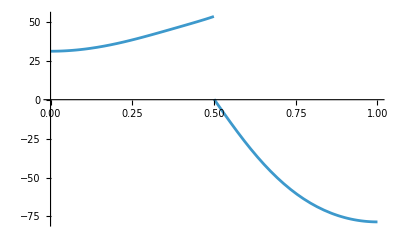

```mathematica
Plot[C2dynNum,{t,0,1}]
```

```mathematica
F3dynNum=F3dyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

2.4 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]] (Piecewise[{{0, t<0}, {0.141022, 0<t<1/2}, {-0.141022, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])+3 (Piecewise[{{0, t<0}, {2.06583, 0<t<1/2}, {-2.06583, 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])-1.5 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]^2 (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])^2-3 Cos[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]^2 (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]) (Piecewise[{{0, t<0}, {0.141022 t, 0<t<1/2}, {-0.0705111 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])^2-1.5 (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])^2-3 (Piecewise[{{0.132456+1.03291 t^2, 0≤t≤1/2}, {0.648913-1.03291 (1-t)^2, 1/2<t≤1}, {0, True}}]) (Piecewise[{{0, t<0}, {11.2794 t, 0<t<1/2}, {-5.63968 (-2.+2 t), 1/2<t<1}, {0, t>1}, {Indeterminate, True}}])^2+29.43 Sin[Piecewise[{{0.321751+5.63968 t^2, 0≤t≤1/2}, {3.14159-5.63968 (1-t)^2, 1/2<t≤1}, {0, True}}]]

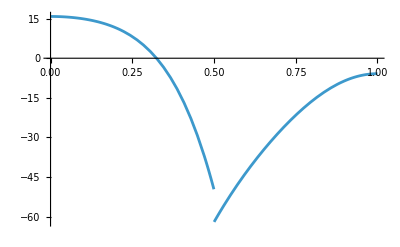

```mathematica
Plot[F3dynNum,{t,0,1}]
```